```mathematica
(* 1 - Botswana, 2 - Zimbabwe *)
(* Human parameters *)
Subscript[N, 1]=1.75 10^5;
Subscript[N, 2]=1.3 10^7;

(* Mosquito parameters *) 
Subscript[M, 1]=1.75 10^6;
Subscript[M, 2]=1.3 10^8;
Subscript[μ, 1]=N@(1/30);
Subscript[μ, 2]=N@(1/10);
Subscript[γ, 1]=N@(1/14);
Subscript[γ, 2]=N@(1/14);
τ=10;

(* Infectivity parameters *)
Subscript[a, 1]=0.082;
Subscript[b, 1]=0;
Subscript[a, 2]=0.241;
Subscript[β, hv]=0.1;
Subscript[β, vh]=0.5;

(* Migration parameters *) 
Subscript[p, 11]=1;
Subscript[p, 12]=1-Subscript[p, 11];
Subscript[p, 22]=1;
Subscript[p, 21]=1-Subscript[p, 22];

(* Control parameters *)
(*κ=0.35;*)
κ=0;
Subscript[u, 1]=0.15;
Subscript[u, 2]=0.3;

Subscript[β, vh] (Subscript[N, 1]-Subscript[x, 1])((Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 1])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 1])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 1] Subscript[x, 1]
Subscript[β, hv] Subscript[a, 1](Subscript[M, 1]-Subscript[y, 1])(Subscript[p, 11](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 21](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2]) - Subscript[μ, 1] Subscript[y, 1]

Subscript[β, vh] (Subscript[N, 2]-Subscript[x, 2])((Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 2])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 2])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 2] Subscript[x, 2]
Subscript[β, hv] Subscript[a, 2](Subscript[M, 2]-Subscript[y, 2])(Subscript[p, 12](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 22](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2]) - Subscript[μ, 2] Subscript[y, 2]
```

-0.0714286 x_1+0.5 (175000.-x_1) (0.+3.35746×10^-7 y_1)

4.68571×10^-8 (0.+1. x_1) (1.75×10^6-y_1)-0.0333333 y_1

-0.0714286 x_2+0.5 (1.3×10^7-x_2) (0.+6.81992×10^-9 y_2)

1.85385×10^-9 (0.+1. x_2) (1.3×10^8-y_2)-0.1 y_2

```mathematica
l={1,2};
l⟦1⟧
```

1

0.967216

```mathematica
Subscript[x, 1]'[t]=Subscript[β, vh] (Subscript[N, 1]-Subscript[x, 1][t])((Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 1])Subscript[y, 1][t])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 1])Subscript[y, 2][t])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 1] Subscript[x, 1][t]
Subscript[y, 1]'[t]=Subscript[β, hv] Subscript[a, 1](Subscript[M, 1]-Subscript[y, 1][t])(Subscript[p, 11](1-κ Subscript[u, 1])Subscript[x, 1][t]+ Subscript[p, 21](1-κ Subscript[u, 2])Subscript[x, 2][t])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2]) - Subscript[μ, 1] Subscript[y, 1][t]

Subscript[x, 2]'[t]=Subscript[β, vh] (Subscript[N, 2]-Subscript[x, 2][t])((Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 2])Subscript[y, 1][t])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 2])Subscript[y, 2][t])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 2] Subscript[x, 2][t]
Subscript[y, 2]'[t]=Subscript[β, hv] Subscript[a, 2](Subscript[M, 2]-Subscript[y, 2][t])(Subscript[p, 12](1-κ Subscript[u, 1])Subscript[x, 1][t]+ Subscript[p, 22](1-κ Subscript[u, 2])Subscript[x, 2][t])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2]) - Subscript[μ, 2] Subscript[y, 2][t]
```

-γ_1 x_1[t]+β_vh (N_1-x_1[t]) ((ⅇ^(-τ μ_1) a_1 p_11 (1-κ u_1) y_1[t])/(N_1 p_11+N_2 p_21)+(ⅇ^(-τ μ_2) a_2 p_12 (1-κ u_1) y_2[t])/(N_1 p_12+N_2 p_22))

```mathematica
NSolve[{Subscript[β, vh] (Subscript[N, 1]-Subscript[x, 1])((Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 1])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 1])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 1] Subscript[x, 1]==0,
Subscript[β, hv] Subscript[a, 1](Subscript[M, 1]-Subscript[y, 1])(Subscript[p, 11](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 21](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2]) - Subscript[μ, 1] Subscript[y, 1]==0,

Subscript[β, vh] (Subscript[N, 2]-Subscript[x, 2])((Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 2])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 2])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 2] Subscript[x, 2]==0,
Subscript[β, hv] Subscript[a, 2](Subscript[M, 2]-Subscript[y, 2])(Subscript[p, 12](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 22](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2]) - Subscript[μ, 2] Subscript[y, 2]==0,
Subscript[x, 1]≥0,Subscript[y, 1]≥0,Subscript[x, 2]≥0,Subscript[y, 2]≥0,Subscript[x, 1]≤Subscript[N, 1],Subscript[y, 1]≤Subscript[M, 1],Subscript[x, 2]≤Subscript[N, 2],Subscript[y, 2]≤Subscript[M, 2]},{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2]},Reals]
```

{{x_1→1637.74,y_1→4019.59,x_2→3.71042×10^6,y_2→8.3666×10^6},{x_1→0.,y_1→0.,x_2→3.71042×10^6,y_2→8.3666×10^6},{x_1→1637.74,y_1→4019.59,x_2→0.,y_2→0.},{x_1→0.,y_1→0.,x_2→0.,y_2→0.}}

```mathematica
NSolve[
Subscript[β, vh] (Subscript[N, 1]-Subscript[x, 1])((Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 1])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 1])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 1] Subscript[x, 1]==0&&
Subscript[β, hv] Subscript[a, 1](Subscript[M, 1]-Subscript[y, 1])(Subscript[p, 11](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 21](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2]) - Subscript[μ, 1] Subscript[y, 1]==0&&

Subscript[β, vh] (Subscript[N, 2]-Subscript[x, 2])((Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 2])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 2])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 2] Subscript[x, 2]==0&&
Subscript[β, hv] Subscript[a, 2](Subscript[M, 2]-Subscript[y, 2])(Subscript[p, 12](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 22](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2]) - Subscript[μ, 2] Subscript[y, 2]==0&&
Subscript[x, 1]≥0&&Subscript[y, 1]≥0&&Subscript[x, 2]≥0&&Subscript[y, 2]≥0&&
Subscript[x, 1]≤Subscript[N, 1]&&Subscript[y, 1]≤Subscript[M, 1]&&Subscript[x, 2]≤Subscript[N, 2]&&Subscript[y, 2]≤Subscript[M, 2],
{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2]},Reals]
```

{{x_1→49482.1,y_1→113810.,x_2→3.67581×10^6,y_2→8.29355×10^6},{x_1→0.,y_1→0.,x_2→0.,y_2→0.}}

```mathematica
n=20;
step=1/n;
(*equilibriumPoints = ConstantArray[0,{n,n}];*)
equilibriumPoints={};
For[i=0,step i≤0.5,i+=1,
For[j=0,step j≤0.5,j+=1,
Subscript[p, 11]=1-step i;
Subscript[p, 12]=1-Subscript[p, 11];
Subscript[p, 22]=1-step j;
Subscript[p, 21]=1-Subscript[p, 22];
(*equilibriumPoints⟦i+1,j+1⟧=*)
AppendTo[equilibriumPoints,(*Association["p_11"->Subscript[p, 11],"p_11"->Subscript[p, 22],"sol"->NSolve[*)
{Subscript[p, 11],Subscript[p, 22],NSolve[
Subscript[β, vh] (Subscript[N, 1]-Subscript[x, 1])((Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 1])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 1])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 1] Subscript[x, 1]==0&&
Subscript[β, hv] Subscript[a, 1](Subscript[M, 1]-Subscript[y, 1])(Subscript[p, 11](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 21](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2]) - Subscript[μ, 1] Subscript[y, 1]==0&&

Subscript[β, vh] (Subscript[N, 2]-Subscript[x, 2])((Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1](1-κ Subscript[u, 2])Subscript[y, 1])/(Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2])+(Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2](1-κ Subscript[u, 2])Subscript[y, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2])) - Subscript[γ, 2] Subscript[x, 2]==0&&
Subscript[β, hv] Subscript[a, 2](Subscript[M, 2]-Subscript[y, 2])(Subscript[p, 12](1-κ Subscript[u, 1])Subscript[x, 1]+ Subscript[p, 22](1-κ Subscript[u, 2])Subscript[x, 2])/(Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2]) - Subscript[μ, 2] Subscript[y, 2]==0&&
Subscript[x, 1]≥0&&Subscript[y, 1]≥0&&Subscript[x, 2]≥0&&Subscript[y, 2]≥0&&
Subscript[x, 1]≤Subscript[N, 1]&&Subscript[y, 1]≤Subscript[M, 1]&&Subscript[x, 2]≤Subscript[N, 2]&&Subscript[y, 2]≤Subscript[M, 2],
{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2]},Reals]
}];
]]
```

```mathematica
(*humanSolutions={Subscript[x, 1],Subscript[x, 2]}/.equilibriumPoints //TableForm*)
humanSolutions = ({#⟦1⟧,#⟦2⟧,{Subscript[x, 1],Subscript[x, 2]}/.(#⟦3⟧⟦1⟧)}&)/@equilibriumPoints;
botswana=({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦1⟧}&)/@humanSolutions;
zimbabwe=({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦2⟧}&)/@humanSolutions;
```

-Graphics3D-

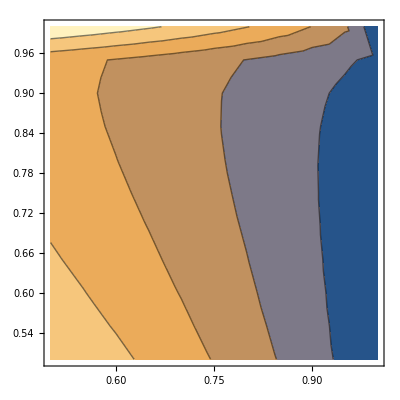

```mathematica
ListPlot3D[botswana]
ListContourPlot[botswana]
```

-Graphics3D-

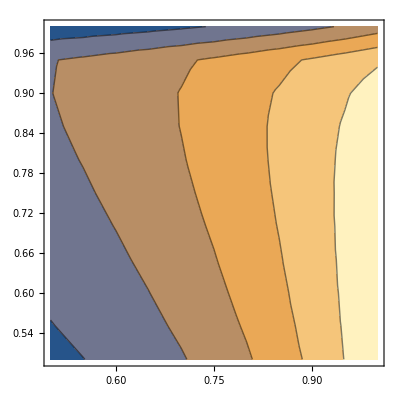

```mathematica
ListPlot3D[zimbabwe]
ListContourPlot[zimbabwe]
```